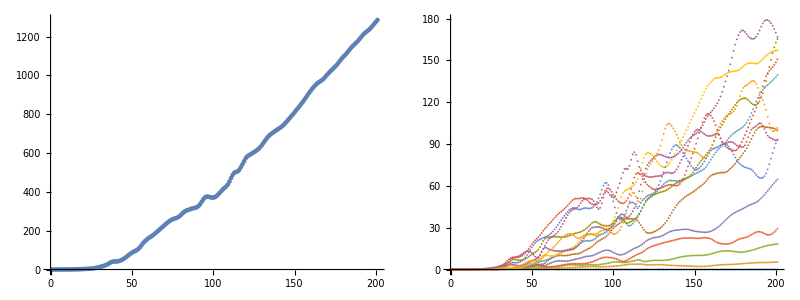

```mathematica
file="/Users/rogeriojorge/local/some_optimizations/GS2_SIMSOPT_ITG/nonlinear_nfp4_QH_initial_ln1.0_lt3.0/gs2Input_ln1.0lt3.0.out.nc";
datasets=Import[file,{"Datasets"}];
flux=Import[file,{"Datasets","es_heat_flux"}]//Transpose;
fluxky=Import[file,{"Datasets","total_es_heat_flux_by_ky"}]//Transpose;
fluxkx=Import[file,{"Datasets","total_es_heat_flux_by_kx"}]//Transpose;
ky=Import[file,{"Datasets","ky"}];kx=Import[file,{"Datasets","kx"}];
Grid[{{ListPlot[flux,ImageSize->Medium],ListPlot[fluxky,ImageSize->Medium]}}]
```

```mathematica
datasets
```

{/density2,/es_mom_flux_perp,/upar,/qparflux_igomega_by_mode,/upar_by_mode,/density_flxsurf_avg,/y,/vpa,/gbdrift0,/ntot,/tpar_by_mode,/bpol,/tperp2,/upar_flxsurf_avg,/qval,/kx,/phi,/qpperpj1_by_mode,/es_energy_exchange_by_mode,/ntot_by_mode,/5,/phi2,/total_es_heat_flux_by_kx,/zref,/es_energy_exchange,/tpar_igomega_by_mode,/eps_trapped,/qpperpj1_igomega_by_mode,/bmag,/tpar2_by_kx,/es_part_tormom_flux,/4,/tprim,/density_igomega_by_mode,/tperp2_by_kx,/pperpj1_by_mode,/total_es_part_flux,/es_heat_flux_par_by_mode,/type,/gds21,/total_es_mom_flux_par_by_kx,/beta,/upar2_by_mode,/nref,/fprim,/rprime,/total_es_heat_flux_perp_by_mode,/total_es_part_flux_by_mode,/phi_norm,/qpperpj1,/temp,/total_es_part_tormom_flux_by_kx,/qpperpj12_by_ky,/vflux_tot,/total_es_mom_flux_by_kx,/gbdrift,/rhoref,/total_es_mom_flux_by_mode,/hflux_tot,/bref,/total_es_heat_flux_par_by_mode,/aref,/tpar2,/es_heat_flux,/species,/upar2,/total_es_mom_flux_perp_by_kx,/pperpj12,/total_es_heat_flux_par,/pperpj12_by_ky,/pperpj1_igomega_by_mode,/total_es_energy_exchange_by_kx,/aprime,/total_es_energy_exchange,/es_mom_flux,/cdrift0,/total_es_energy_exchange_by_ky,/zplot,/phi_corr_2pi,/es_mom_flux_par,/upar2_by_kx,/layout,/ntot2_by_ky,/qparflux_flxsurf_avg,/es_heat_flux_perp,/jacob,/cvdrift,/theta,/total_es_energy_exchange_by_mode,/tpar2_by_mode,/tperp2_by_mode,/density,/total_es_mom_flux_par,/total_es_mom_flux_perp_by_mode,/rplot,/phi_igomega_by_mode,/drhodpsi,/es_part_flux,/zprime,/qparflux2_by_kx,/total_es_heat_flux_perp_by_kx,/dens,/qpperpj12_by_mode,/es_mom_flux_perp_by_mode,/total_es_mom_flux_par_by_ky,/gds2,/shat,/total_es_part_tormom_flux,/ky,/total_es_heat_flux,/tpar_flxsurf_avg,/qpperpj1_flxsurf_avg,/grho,/tperp_flxsurf_avg,/total_es_mom_flux_by_ky,/mref,/phi2_by_ky,/total_es_heat_flux_perp_by_ky,/energy,/total_es_heat_flux_par_by_ky,/qparflux2,/es_heat_flux_perp_by_mode,/upar2_by_ky,/mom_flux_tot,/input_file,/vnewk,/total_es_part_flux_by_kx,/gradpar,/ri,/omega,/es_part_flux_by_mode,/cvdrift0,/phi2_by_kx,/ntot_igomega_by_mode,/charge,/gds24,/tperp_igomega_by_mode,/total_es_mom_flux_par_by_mode,/ntot2_by_mode,/es_heat_flux_by_mode,/omega_average,/ntot2_by_kx,/gds22,/total_es_mom_flux_perp,/2,/vref,/upar_igomega_by_mode,/ntot2,/pperpj12_by_mode,/es_mom_flux_par_by_mode,/3,/t,/qparflux2_by_mode,/total_es_mom_flux_perp_by_ky,/total_es_part_tormom_flux_by_mode,/qparflux2_by_ky,/tperp_by_mode,/tref,/heat_flux_tot,/pperpj1_flxsurf_avg,/qpperpj12,/qpperpj12_by_kx,/pperpj1,/theta0,/total_es_heat_flux_by_mode,/density2_by_kx,/input_file_dim,/uprim,/mass,/es_flux_vs_e,/aplot,/qparflux,/density_by_mode,/total_es_mom_flux,/es_mom_flux_by_mode,/density2_by_ky,/zflux_tot,/density2_by_mode,/tperp,/phi2_by_mode,/total_es_heat_flux_par_by_kx,/theta_ext,/gds23,/ntot_flxsurf_avg,/total_es_heat_flux_perp,/tpar2_by_ky,/tperp2_by_ky,/qparflux_by_mode,/cdrift,/total_es_part_flux_by_ky,/es_part_tormom_flux_by_mode,/es_heat_flux_par,/phase,/total_es_part_tormom_flux_by_ky,/part_flux_tot,/total_es_heat_flux_by_ky,/tpar,/x,/pperpj12_by_kx,/lambda,/gds24_noq}